## Page-Wootters model: NN-level clock + 2-level system

```mathematica
NN= 2
```

2

```mathematica
(* T := DiagonalMatrix[Range[0,NN-1]] *)
```

```mathematica
F := FourierMatrix[NN]
```

```mathematica
Ω := ⅈ*{{0,1}, {-1,0}}
```

```mathematica
T:= F†.Ω.F
```

```mathematica
T
```

{{0,-ⅈ},{ⅈ,0}}

Hamiltonian in "ordinary" space

```mathematica
Hs := ⅈ{{0,1},{-1,0}}
```

```mathematica
MatrixForm[Hs]
```

(0 | ⅈ
-ⅈ | 0)

Matrix representation of eq. (1) in https://arxiv.org/abs/1504.04215 by Lloyd, Giovannetti and Maccone.
We turn it into numeric as treating  it symbolically onwards would be unfeasible.

```mathematica
J := N[KroneckerProduct[Ω,IdentityMatrix[2]] + KroneckerProduct[IdentityMatrix[NN],Hs]]
```

```mathematica
Chop[Eigenvalues[J]]
```

{-2.,2.,0,0}

```mathematica
chosenEigenvector := Eigenvectors[J][[ 4]]

chosenProbUnnormalized := Abs[chosenEigenvector^2]
```

```mathematica
Normalization := chosenProbUnnormalized[[1]] + chosenProbUnnormalized[[2]]
```

```mathematica
probability := chosenProbUnnormalized / Normalization
```

```mathematica
probability
```

{0.,1.,1.,0.}

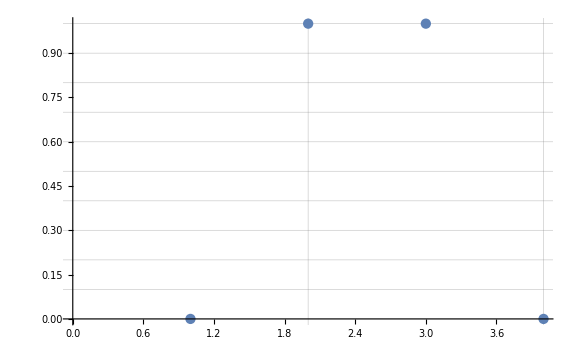

```mathematica
ListPlot[probability, GridLines ->{Range[0,NN*2, 2], Range[0,1,0.1]}, ImageSize->Large]
```

Consistency of PW with ordinary QM (discrete approximation):

Ordinary quantum mechanics time evolution, with initial state  (1-i)/2 * |0>  + (1+i)/2 |1>

```mathematica
psi[t_] := MatrixExp[-ⅈ Hs t, {(1/2)-(1/2)ⅈ,(1/2)+(1/2)ⅈ} ]
```

```mathematica
psi[t]
```

{(1/2-ⅈ/2) Cos[t]+(1/2+ⅈ/2) Sin[t],(1/2+ⅈ/2) Cos[t]-(1/2-ⅈ/2) Sin[t]}

Picking 8 samples, equally spaced from 0 to 2π (excluding 2π)

```mathematica
Map[psi, Range[0,(7/4)π,π/4]]
```

{{1/2-ⅈ/2,1/2+ⅈ/2},{1/(√2),ⅈ/(√2)},{1/2+ⅈ/2,-1/2+ⅈ/2},{ⅈ/(√2),-1/(√2)},{-1/2+ⅈ/2,-1/2-ⅈ/2},{-1/(√2),-ⅈ/(√2)},{-1/2-ⅈ/2,1/2-ⅈ/2},{-ⅈ/(√2),1/(√2)}}

This discrete time evolution (samples from an ordinary QM result) coincides with the eigenvector of J related to eigenvalue 0 (PW model result).

```mathematica
Eigensystem[Hs]
```

{{-1,1},{{-ⅈ,1},{ⅈ,1}}}